```mathematica
PerfectDistanceQ[G_]:=(Union@*Flatten@*Round@GraphDistanceMatrix[G] == Range[0,Binomial[VertexCount[G],2]]);

EdgeWeights[G_]:=AnnotationValue[G,EdgeWeight];
(*TODO: NoNewVertex[G] avoid edges connecting vertices with distance less than NextWeight[G]. Use triangle inequality to prove that adding an edge 
v1<->v2 with weight w can only yield a graph with NON-MINIMAL decendants.*)
NoNewVertex[G_]:=#1<->#2&@@@Position[UpperTriangularize[GraphDistanceMatrix[G]],d_/;NextWeight[G]<d]
OneNewVertex[G_]:=#<->(VertexCount[G]+1)&/@ VertexList[G]
TwoNewVertex[G_]:={(VertexCount[G]+1)<->(VertexCount[G]+2)}
NewEdges[G_]:=Join[NoNewVertex[G],OneNewVertex[G],TwoNewVertex[G]];
NextWeight[G_]:=
Module[{distances,nextWeight},
distances =DeleteCases[Union@*Flatten@*Round@*GraphDistanceMatrix@*Graph@G,0];nextWeight = Max[EdgeWeights[G]]+1;While[(nextWeight<=Length[distances])∧(distances[[nextWeight]]==nextWeight),nextWeight++];
nextWeight
]

AddWeightedEdge[G_,e_,w_]:=Graph[EdgeAdd[G,e],EdgeWeight->Append[EdgeWeights[G],w]]

(*TODO: Redefine Children[G] using a module combining NextWeight, NewEdges and GoodChildQ to reduce redundant computations and function calls*)
Children[G_]:=AddWeightedEdge[G,#,NextWeight[G]]&/@NewEdges[G];

(*Computes Children of G in search for Minimal PDGs. Attempting to avoid redundant function calls e.g. computations of GraphDistanceMatrix*)
FastChildren[G_,n_,PDGs_]:=Module[ {vertexCount,edgeCount,vertexList, edgeList, weightList, graphDistanceMatrix,distances,distancesDuplicateFree,newWeight,validNewEdges,GoodChildQ,allChildren,goodChildren},
(*Important values and lists*)
vertexCount=VertexCount[G];
edgeCount = EdgeCount[G];
vertexList = VertexList[G];
edgeList = EdgeList[G];
weightList = AnnotationValue[G,EdgeWeight];
(*GraphDistanceMatrix and associated distances(does not remove duplicates) and distancesDuplicateFree.*)
graphDistanceMatrix = GraphDistanceMatrix[G];
distances= DeleteCases[Flatten@*Round@graphDistanceMatrix,0];
distancesDuplicateFree = Union@distances;
(*Compute newWeight*)
newWeight = Max[weightList]+1;
While[(newWeight<=Length[distancesDuplicateFree])∧(distancesDuplicateFree[[newWeight]]==newWeight),newWeight++];
(*Compute validNewEdges*)
validNewEdges = Join[#1<->#2&@@@Position[UpperTriangularize[graphDistanceMatrix],d_/;newWeight<d],  #<->(vertexCount+1)&/@ vertexList,{(vertexCount+1)<->(vertexCount+2)}];
(*Compute allChildren*)
allChildren = Graph[EdgeAdd[G,#],EdgeWeight->Append[weightList,newWeight]]&/@validNewEdges;
(*Define FastGoodChildQ*)
GoodChildQ[Gchild_]:= (VertexCount[Gchild] <=n) ∧(SubsetQ[Range[Binomial[n,2]],AnnotationValue[Gchild,EdgeWeight]])∧(AllTrue[First/@Select[Tally@DeleteCases[Flatten@GraphDistanceMatrix[Gchild],0.],Last[#]>2&],NextWeight[Gchild]<=#&])∧(Not[AnyTrue[PDGs,IsomorphicSubgraphQ[#,Gchild]&]]);

(* Reducing allChildren to goodChildren*)
goodChildren = DeleteDuplicates[Select[allChildren,GoodChildQ],LineGraph[#1]==LineGraph[#2]&&IsomorphicGraphQ[#1,#2]&];
goodChildren
]
```

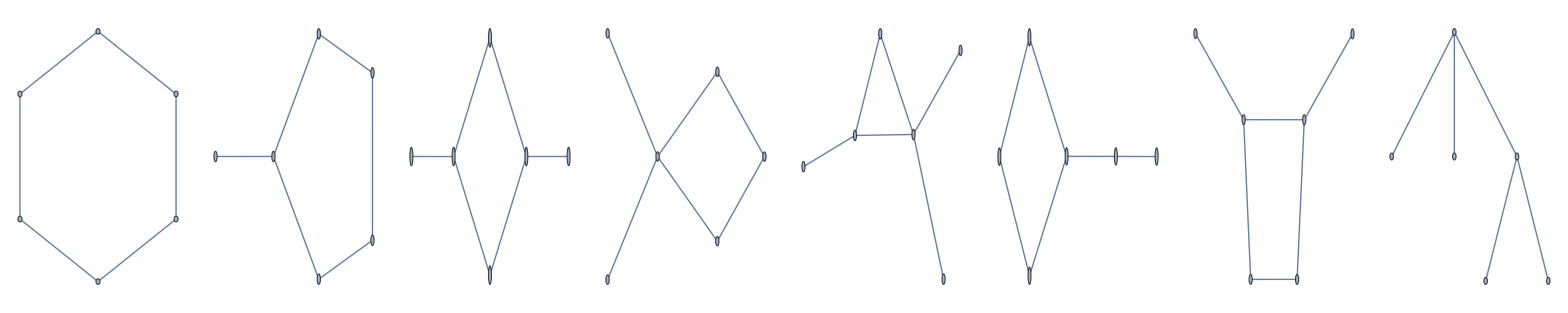
Time To Compute:	00:00:04TimeObject[{0,0,4.84739},Instant] and 847.39ms
Almost Minimal Perfect Distance Graphs(8): 
-Graphics-

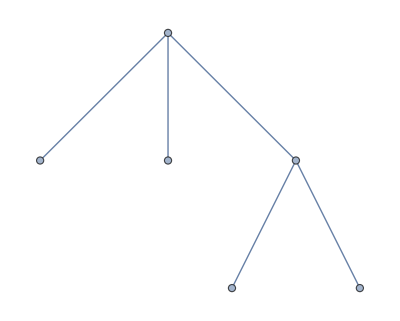
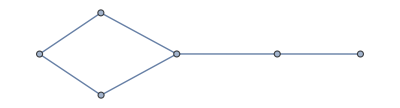
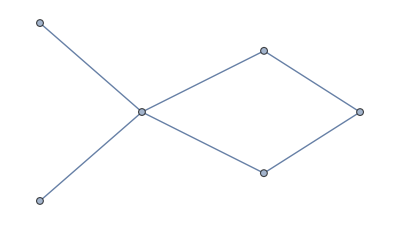
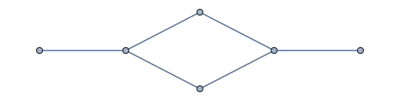
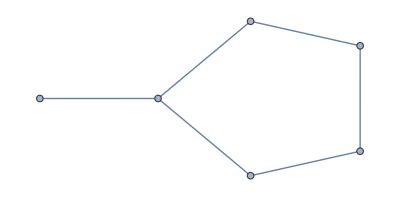
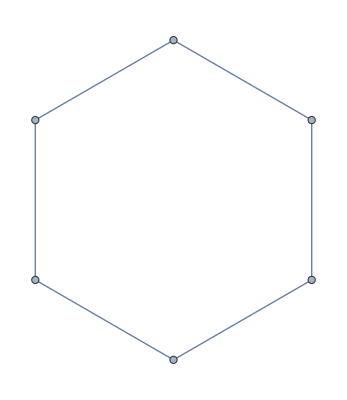

```mathematica
n =6;

GoodChildQ[G_]:=(VertexCount[G] <=n) ∧(SubsetQ[Range[Binomial[n,2]],EdgeWeights[G]])∧(AllTrue[First/@Select[Tally@DeleteCases[Flatten@GraphDistanceMatrix[G],0.],Last[#]>2&],NextWeight[G]<=#&])∧(Not[AnyTrue[PDGs,IsomorphicSubgraphQ[#,G]&]]);

PDGs = {};
stack =CreateDataStructure["Stack"];
Gstart = Graph[{1<->2},EdgeWeight->{1<->2->1}];

stack["Push",Gstart];

TotalTime = AbsoluteTiming[
(*Depth First Search*)
Until[stack["EmptyQ"],
G = stack["Pop"];
If[(VertexCount[G]==n ∧ PerfectDistanceQ[G]),
AppendTo[PDGs,G];
,(*Else*)
children =DeleteDuplicates[Select[Children[G],GoodChildQ],LineGraph[#1]==LineGraph[#2]&&IsomorphicGraphQ[#1,#2]&];
Do[stack["Push",g],{g,children}];
]
];

][[1]];
Print[
"Time To Compute:\t",TimeObject[{0,0,TotalTime}]," and ",1000FractionalPart[TotalTime],"ms\n",
"Almost Minimal Perfect Distance Graphs(",Length[PDGs],"): \n",TableForm[PDGs,TableDirections->Row],"\n"
]
sortedPDGs = SortBy[PDGs,EdgeCount];
reducedPDGs = sortedPDGs;
Do[reducedPDGs = DeleteDuplicatesBy[reducedPDGs,If[IsomorphicSubgraphQ[G,#],G,#]&],{G,sortedPDGs}]
reducedPDGs
```

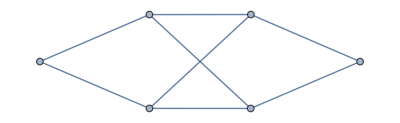
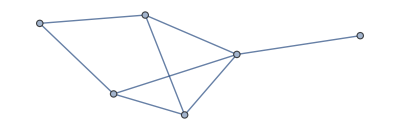
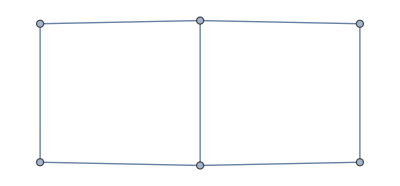
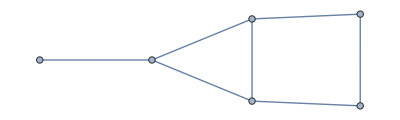
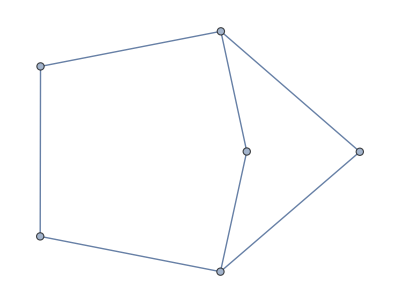
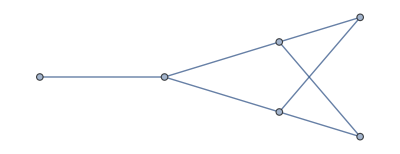
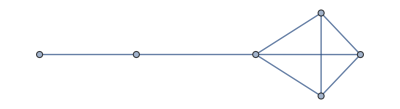
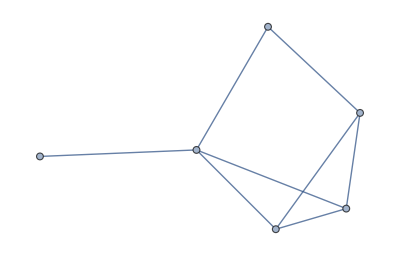
Time To Compute:	00:00:04TimeObject[{0,0,4.94658},Instant] and 946.58ms
Almost Minimal Perfect Distance Graphs(22): 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
n =6;

PDGs = {};
stack =CreateDataStructure["Stack"];
Gstart = Graph[{1<->2},EdgeWeight->{1<->2->1}];

stack["Push",Gstart];

TotalTime = AbsoluteTiming[
(*Depth First Search*)
Until[stack["EmptyQ"],
G = stack["Pop"];
If[(VertexCount[G]==n ∧ PerfectDistanceQ[G]),
AppendTo[PDGs,G];
,(*Else*)
children =FastChildren[G,n,PDGs];
stack["PushList",children];
]
];

][[1]];
Print[
"Time To Compute:\t",TimeObject[{0,0,TotalTime}]," and ",1000FractionalPart[TotalTime],"ms\n",
"Almost Minimal Perfect Distance Graphs(",Length[PDGs],"): \n",TableForm[PDGs,TableDirections->Row],"\n"
]
sortedPDGs = SortBy[PDGs,EdgeCount];
reducedPDGs = sortedPDGs;
Do[reducedPDGs = DeleteDuplicatesBy[reducedPDGs,If[IsomorphicSubgraphQ[G,#],G,#]&],{G,sortedPDGs}]
reducedPDGs
```